```mathematica
zero={{0,0},{0,0}};
```

{{0,0},{0,0}}

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

```mathematica
A=DiagonalMatrix[{a,a}];
B=DiagonalMatrix[{b,b}];
Cc=DiagonalMatrix[{cp,cm}];
```

```mathematica
(σ[a_,b_,cp_,cm_]=ArrayFlatten[{{A,Cc},{Cc,B}}])//MatrixForm
```

(a | 0 | cp | 0
0 | a | 0 | cm
cp | 0 | b | 0
0 | cm | 0 | b)

```mathematica
s=Table[RandomReal[{1,10}],{i,10^4}];
d=Table[RandomReal[{1-s[[i]],s[[i]]-1}],{i,10^4}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,100}],{i,10^4}];
λ=Table[RandomReal[{-1,1}],{i,10^4}];

a=Table[s[i]+d[i],{i,10^4}];
b=Table[s[i]-d[i],{i,10^4}];

cp=Table[
[1/[4sqrt[[s[i]]^2-[d[i]]^2]]]*[[sqrt[[4[d[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]-4[g[i]]^2]+[sqrt[4[s[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]]
,{i,10^4}];

cm=Table[
[1/[4sqrt[[s[i]]^2-[d[i]]^2]]]*[[sqrt[[4[d[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]-4[g[i]]^2]-[sqrt[4[s[i]]^2+[1/2][[g[i]]^2+1][λ[i]-1]-[2[d[i]]^2+g[i]][λ[i]+1]]^2]]
,{i,10^4}];
```

```mathematica
s[[1]]
```

8.68833

```mathematica
d[[1]]
```

-2.12824

```mathematica
a[[1]]
```

{-2.12824,-1.888,-1.80044,0.507144,4.21114,-1.4073,-4.15281,-2.46486,-2.84643,-2.39145,0.0247638,9978,-4.33334,-2.91275,-0.355147,0.345103,-0.803702,0.666211,-1.20699,0.155515,-1.34414,0.156537,-7.25642}[1]+{1}[1]
 |  |  |  |

```mathematica
b[[1]]
```

-{-2.12824,-1.888,-1.80044,0.507144,4.21114,-1.4073,-4.15281,-2.46486,-2.84643,-2.39145,0.0247638,9978,-4.33334,-2.91275,-0.355147,0.345103,-0.803702,0.666211,-1.20699,0.155515,-1.34414,0.156537,-7.25642}[1]+{1}[1]
 |  |  |  |

```mathematica
covm=Table[σ[a[[i]],b[[i]],cp[[i]],cm[[i]]],{i,10^4}];
```

Part::partd: Part specification cp⟦1⟧ is longer than depth of object.

Part::partd: Part specification cm⟦1⟧ is longer than depth of object.

Part::partd: Part specification cp⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of {2.02499,3.53499,1.72424,6.15681,1.22956,6.69833,-3.4883,-5.57146,-3.21396,-0.612861,4.51232,1.05686,-2.65685,«26»,1.95375,1.17957,0.101783,0.117964,7.25683,-3.14153,-1.17108,-0.9007,-5.87795,-5.0262,1.3221,«9950»}[3]+{«1»}[3] does not exist.

Part::partw: Part 3 of -{2.02499,3.53499,1.72424,6.15681,1.22956,6.69833,-3.4883,-5.57146,-3.21396,-0.612861,4.51232,1.05686,-2.65685,«26»,1.95375,1.17957,0.101783,0.117964,7.25683,-3.14153,-1.17108,-0.9007,-5.87795,-5.0262,1.3221,«9950»}[3]+{«1»}[3] does not exist.

Part::partw: Part 4 of {2.02499,3.53499,1.72424,6.15681,1.22956,6.69833,-3.4883,-5.57146,-3.21396,-0.612861,4.51232,1.05686,-2.65685,«26»,1.95375,1.17957,0.101783,0.117964,7.25683,-3.14153,-1.17108,-0.9007,-5.87795,-5.0262,1.3221,«9950»}[4]+{«1»}[4] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
covm[[4]]
```

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Min[Eigenvalues[covm[[i]]]],Min[Eigenvalues[covm[[i]]+ⅈ Σ]],Min[Abs[Eigenvalues[ⅈ Σ . covm[[i]]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

10000

```mathematica
phystest[[560]]
```

{0.546685,0.399842,1.98739}

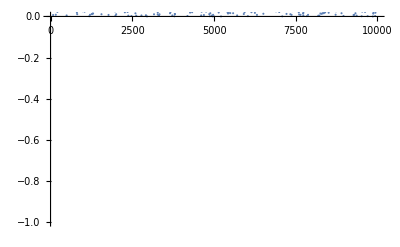

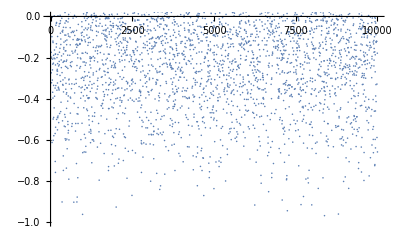

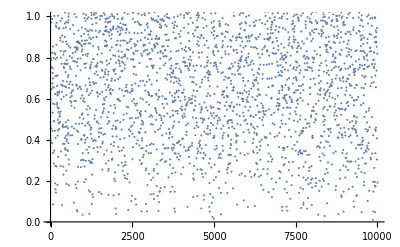

```mathematica
ListPlot[Table[phystest[[i,1]],{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[phystest[[i,2]],{i,1,Length[cm]}],PlotRange->{-1,0}]
ListPlot[Table[phystest[[i,3]],{i,1,Length[cm]}],PlotRange->{0,1}]
```

```mathematica
Clear[cm]
```

```mathematica
Eigenvalues[σ[a,b,cp,cm]]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+4 cm^2)),1/2 (a+b+√((a-b)^2+4 cm^2)),1/2 (a+b-√((a-b)^2+4 cp^2)),1/2 (a+b+√((a-b)^2+4 cp^2))}

```mathematica
Eigenvalues[σ[a,b,cp,cm]+ⅈ Σ]//FullSimplify
```

{1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2-√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b-√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2)))),1/2 (a+b+√((a-b)^2+2 (2+cm^2+cp^2+√(4 (a-b)^2+(4+(cm-cp)^2) (cm+cp)^2))))}

```mathematica
Eigenvalues[ⅈ Σ . σ[a,b,cp,cm]]//FullSimplify
```

{-(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp-√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),-(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2),(ⅈ √(-a^2-b^2-2 cm cp+√(a^4+b^4+4 b^2 cm cp-2 a^2 (b^2-2 cm cp)+4 a b (cm^2+cp^2))))/(√2)}